```mathematica
TI4=Import["~/TI4_networth.ods"]
TI5={{0,1.6},{1,3.527102},{2,4.551752},{3,5.131860},{4,5.599591}};
```

{{{0,1.6},{1,2.68206},{2,3.41239},{3,3.8871},{4,4.35937},{5,4.75109},{6,5.03224},{7,5.29374},{8,5.55666},{9,5.75748},{10,5.92025},{11,6.07707},{12,6.23797},{13,6.36256},{14,6.49109},{15,6.6269},{16,6.73067},{17,6.82937},{18,6.91624},{19,6.99377},{20,7.07259},{21,7.14956},{22,7.8206},{23,8.10829},{24,8.31126},{25,8.48072},{26,8.61333},{27,8.72916},{28,8.84857},{29,8.9456},{30,9.04259},{31,9.12841},{32,9.2107},{33,9.28734},{34,9.34587},{35,9.40875},{36,9.47995},{37,9.53958},{38,9.59331},{39,9.6054},{40,9.64929},{41,9.69444},{42,9.7442},{43,9.79523},{44,9.84048},{45,9.88047},{46,9.91621},{47,9.95143},{48,9.98317},{49,10.0193},{50,10.059},{51,10.0952},{52,10.1247},{53,10.2029},{54,10.252},{55,10.2941},{56,10.3552},{57,10.4038},{58,10.4455},{59,10.4826},{60,10.5254},{61,10.5669},{62,10.6049},{63,10.6454},{64,10.6846},{65,10.7204},{66,10.7487},{67,10.7801},{68,10.8072},{69,10.829},{70,10.8583},{71,10.8897},{72,10.9224},{73,10.9311}}}

```mathematica
TI4Period1={{0,1.6},{1,2.682056},{2,3.412386},{3,3.887103},{4,4.359369},{5,4.75109},{6,5.032238},{7,5.293739},{8,5.556659},{9,5.757481},{10,5.920247},{11,6.077071},{12,6.237971},{13,6.362555},{14,6.491085},{15,6.626895},{16,6.730669},{17,6.829365},{18,6.916236},{19,6.993768},{20,7.072585},{21,7.149563}};
TI4Period2={{21,7.149563},{22,7.820603},{23,8.108294},{24,8.311263},{25,8.480723},{26,8.613332},{27,8.729162},{28,8.84857},{29,8.945598},{30,9.042588},{31,9.128411},{32,9.210697},{33,9.287343},{34,9.345867},{35,9.40875},{36,9.479952},{37,9.53958},{38,9.593305},{39,9.605399},{40,9.649285}};
TI4Period3={{41,9.69444},{42,9.744198},{43,9.795226},{44,9.84048},{45,9.880467},{46,9.916212},{47,9.951433},{48,9.983165},{49,10.019255},{50,10.059037},{51,10.095225},{52,10.124692}};
TI4Period4={{53,10.202874},{54,10.252018},{55,10.294087},{56,10.355167},{57,10.40384},{58,10.445503},{59,10.482631},{60,10.52542},{61,10.566884},{62,10.604889},{63,10.645383},{64,10.68461}};
TI4Period5={{65,10.720393},{66,10.748667},{67,10.780082},{68,10.807186},{69,10.829017},{70,10.858302},{71,10.889695},{72,10.922374},{73,10.931105}};
```

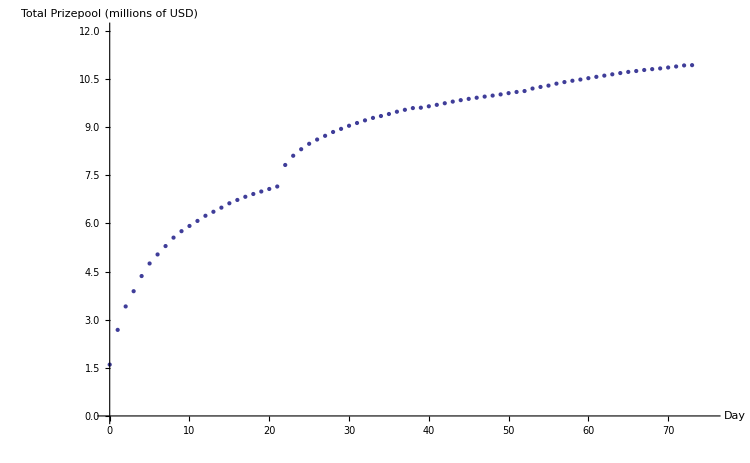

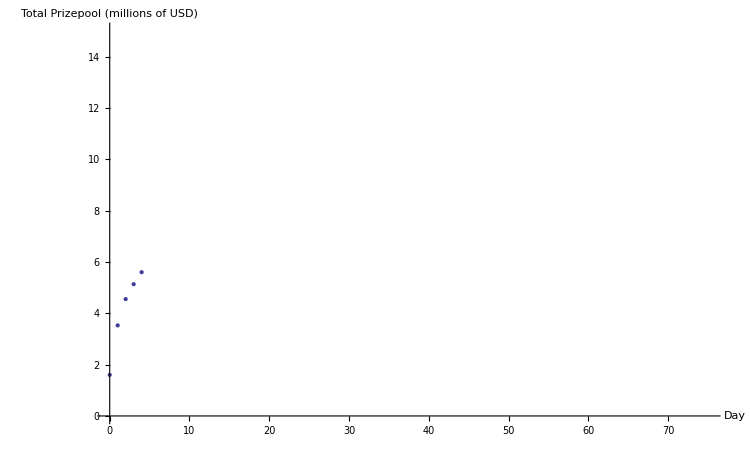

```mathematica
TI4Plot=ListPlot[TI4,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Total Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,75},{0,12}}]
TI5Plot=ListPlot[TI5,Joined->False,LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Total Prizepool (millions of USD)"},ImageSize->150*{5,3},PlotRange->{{0,75},{0,15}}]
```

```mathematica
func=a*x^4+b*x^3+c*x^2+d*x+e
dfunc=D[func,x]
Exp1=FindFit[TI4Period1,a*x^4+b*x^3+c*x^2+d*x+1.6,{a,b,c,d},x]
Exp2=FindFit[TI4Period2,a*x^4+b*x^3+c*x^2+d*x+e,{a,b,c,d,e},x]
Exp3=FindFit[TI4Period3,a*x^4+b*x^3+c*x^2+d*x+e,{a,b,c,d,e},x]
Exp4=FindFit[TI4Period4,a*x^4+b*x^3+c*x^2+d*x+e,{a,b,c,d,e},x]
Exp5=FindFit[TI4Period5,a*x^4+b*x^3+c*x^2+d*x+e,{a,b,c,d,e},x]
Exp1P=func/.a->-0.00009175655814296019/.b->0.004909885230190869/.c->-0.09871636359077875/.d->1.0189842487968803/.e->1.6;
Exp2P=func/.a->-0.00003372074476766601/.b->0.004430134883636133/.c->-0.21957619602814346/.d->4.939819208768745/.e->-33.83552673746016;
Exp3P=func/.a->-0.000012480150057728178/.b->0.002442781622210659/.c->-0.17926658817029845/.d->5.881122935376198/.e->-63.17947733697512;
Exp4P=func/.a->0.000019782415500637082/.b->-0.0045866726397318005/.c->0.3974268810343637/.d->-15.207891495595142/.e->226.60536678832858;
Exp5P=func/.a->-0.0001243409091123275/.b->0.03419099158846598/.c->-3.523908440018641/.d->161.36660099955947/.e->-2759.7351219195134;
PExp1=Plot[Exp1P,{x,0,21}];
PExp2=Plot[Exp2P,{x,22,40}];
PExp3=Plot[Exp3P,{x,41,52}];
PExp4=Plot[Exp4P,{x,53,64}];
PExp5=Plot[Exp5P,{x,65,73}];
logfunc=a*Log[x+1]+b
TI4Log1=FindFit[TI4Period1,logfunc,{a,b},x]
TI4Log2=FindFit[TI4Period2,(c*x+d*x^2+f*x^3)*logfunc,{a,b,c,d,f},x]
TI4Log3=FindFit[TI4Period3,logfunc,{a,b},x]
TI4Log4=FindFit[TI4Period4,logfunc,{a,b},x]
TI4Log5=FindFit[TI4Period5,logfunc,{a,b},x]
Log1P=logfunc/.a->1.85749449353801/.b->1.4411444792583545;
Log2P=(c*x+d*x^2+f*x^3)*logfunc/.a->1.4257190503576913/.b->-2.9501135308111066/.c->0.5832982441844798/.d->-0.02101571487189187/.f->0.00022561730676707757;
Log3P=logfunc/.a->1.8190033666536505/.b->2.907465261562042;
Log4P=logfunc/.a->2.5919660222127385/.b->-0.13106076867972527;
Log5P=logfunc/.a->1.905518782007535/.b->2.737579356042067;
PLog1=Plot[Log1P,{x,0,21}];
PLog2=Plot[Log2P,{x,21,40}];
PLog3=Plot[Log3P,{x,41,52}];
PLog4=Plot[Log4P,{x,53,64}];
PLog5=Plot[Log5P,{x,65,73}];
```

e+d x+c x^2+b x^3+a x^4

d+2 c x+3 b x^2+4 a x^3

{a→-0.0000917566,b→0.00490989,c→-0.0987164,d→1.01898}

{a→-0.0000815772,b→0.0105239,c→-0.507242,d→10.9029,e→-79.6082}

{a→-0.0000124802,b→0.00244278,c→-0.179267,d→5.88112,e→-63.1795}

{a→0.0000197824,b→-0.00458667,c→0.397427,d→-15.2079,e→226.605}

{a→-0.000124341,b→0.034191,c→-3.52391,d→161.367,e→-2759.74}

b+a Log[1+x]

{a→1.85749,b→1.44114}

{a→1.42572,b→-2.95011,c→0.583298,d→-0.0210157,f→0.000225617}

{a→1.819,b→2.90747}

{a→2.59197,b→-0.131061}

{a→1.90552,b→2.73758}

```mathematica
TI4raw={{0,1.6},{1,2.682056},{2,3.412386},{3,3.887103},{4,4.359369},{5,4.75109},{6,5.032238},{7,5.293739},{8,5.556659},{9,5.757481},{10,5.920247},{11,6.077071},{12,6.237971},{13,6.362555},{14,6.491085},{15,6.626895},{16,6.730669},{17,6.829365},{18,6.916236},{19,6.993768},{20,7.072585},{21,7.149563},{22,7.820603},{23,8.108294},{24,8.311263},{25,8.480723},{26,8.613332},{27,8.729162},{28,8.84857},{29,8.945598},{30,9.042588},{31,9.128411},{32,9.210697},{33,9.287343},{34,9.345867},{35,9.40875},{36,9.479952},{37,9.53958},{38,9.593305},{39,9.605399},{40,9.649285},{41,9.69444},{42,9.744198},{43,9.795226},{44,9.84048},{45,9.880467},{46,9.916212},{47,9.951433},{48,9.983165},{49,10.019255},{50,10.059037},{51,10.095225},{52,10.124692},{53,10.202874},{54,10.252018},{55,10.294087},{56,10.355167},{57,10.40384},{58,10.445503},{59,10.482631},{60,10.52542},{61,10.566884},{62,10.604889},{63,10.645383},{64,10.68461},{65,10.720393},{66,10.748667},{67,10.780082},{68,10.807186},{69,10.829017},{70,10.858302},{71,10.889695},{72,10.922374},{73,10.931105}}
```

{{0,1.6},{1,2.68206},{2,3.41239},{3,3.8871},{4,4.35937},{5,4.75109},{6,5.03224},{7,5.29374},{8,5.55666},{9,5.75748},{10,5.92025},{11,6.07707},{12,6.23797},{13,6.36256},{14,6.49109},{15,6.6269},{16,6.73067},{17,6.82937},{18,6.91624},{19,6.99377},{20,7.07259},{21,7.14956},{22,7.8206},{23,8.10829},{24,8.31126},{25,8.48072},{26,8.61333},{27,8.72916},{28,8.84857},{29,8.9456},{30,9.04259},{31,9.12841},{32,9.2107},{33,9.28734},{34,9.34587},{35,9.40875},{36,9.47995},{37,9.53958},{38,9.59331},{39,9.6054},{40,9.64929},{41,9.69444},{42,9.7442},{43,9.79523},{44,9.84048},{45,9.88047},{46,9.91621},{47,9.95143},{48,9.98317},{49,10.0193},{50,10.059},{51,10.0952},{52,10.1247},{53,10.2029},{54,10.252},{55,10.2941},{56,10.3552},{57,10.4038},{58,10.4455},{59,10.4826},{60,10.5254},{61,10.5669},{62,10.6049},{63,10.6454},{64,10.6846},{65,10.7204},{66,10.7487},{67,10.7801},{68,10.8072},{69,10.829},{70,10.8583},{71,10.8897},{72,10.9224},{73,10.9311}}

{a→2.44804,b→0.390211}

0.390211+2.44804 Log[1+x]

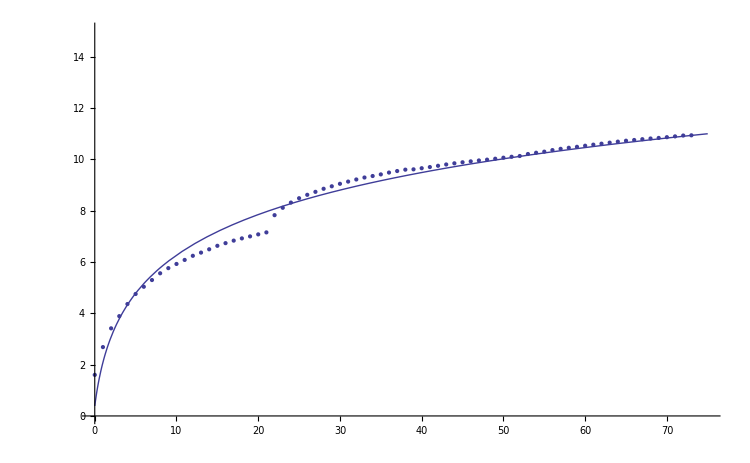

```mathematica
FindFit[TI4raw,logfunc,{a,b},x]
TI4LogOverall=logfunc/.a->2.4480352663396787/.b->0.3902106121898738
PTI4Overall=Plot[TI4LogOverall,{x,0,75}];
Show[{PTI4Overall,TI4Plot},PlotRange->{{0,75},{0,15}},ImageSize->150*{5,3}]
```

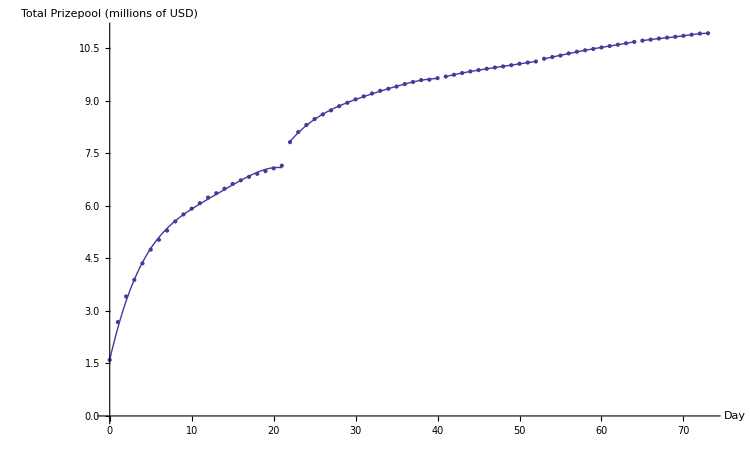

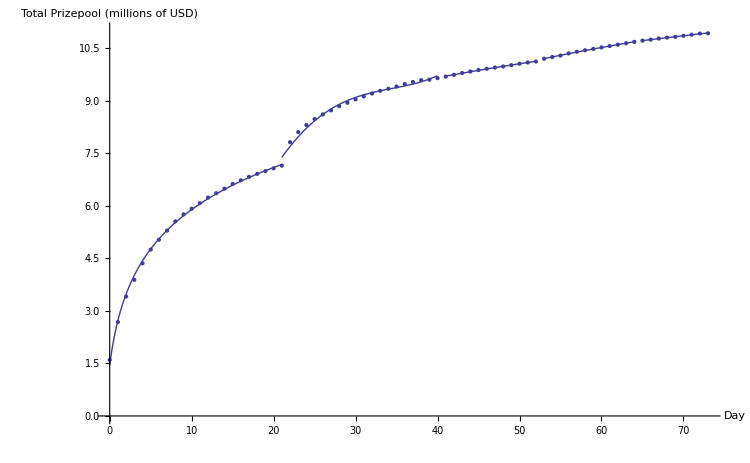

```mathematica
Show[{TI4Plot,PExp1,PExp2,PExp3,PExp4,PExp5},PlotRange->{0,11}]
Show[{TI4Plot,PLog1,PLog2,PLog3,PLog4,PLog5},PlotRange->{0,11}]
```

```mathematica
yint=1.6;
prop1=1.45;
TI5prop=prop1*Exp1P-(prop1*yint-yint);
TI5PropPlot=Plot[TI5prop,{x,0,21},PlotRange->{{0,75},{0,15}}];
TI5logx=FindFit[TI5,logfunc,{a,b},x]
TI5logfunc=a*Log[x+1]+b/.a->2.4940069663929556/.b->1.6940534483905654
TI5Logplot=Plot[TI5logfunc,{x,0,73},PlotRange->{{0,75},{0,15}}];
TI5logfunc/.x->21
```

{a→2.49401,b→1.69405}

1.69405+2.49401 Log[1+x]

9.40313

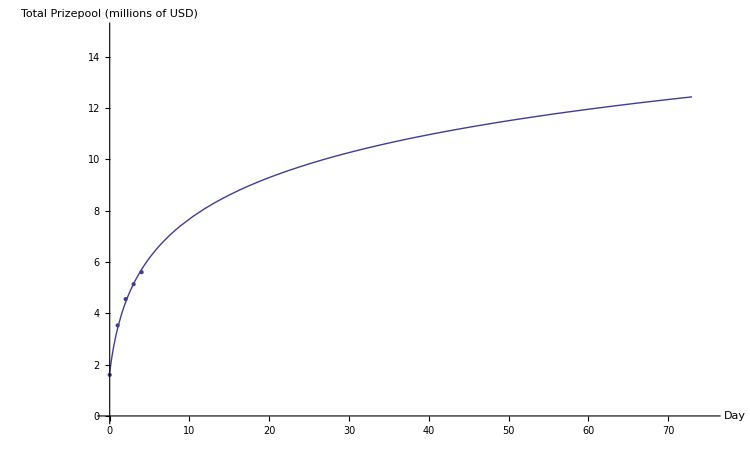

```mathematica
Show[{TI5Plot,TI5Logplot}]
```

```mathematica
FullSimplify[TI5logfunc/Log1P]
```

1.34267-0.129708/(0.775854+1. Log[1+x])

1.34267

1.34267 (0.583298 x-0.0210157 x^2+0.000225617 x^3) (-2.95011+1.42572 Log[1+x])

1.34267 (2.90747+1.819 Log[1+x])

1.34267 (-0.131061+2.59197 Log[1+x])

1.34267 (2.73758+1.90552 Log[1+x])

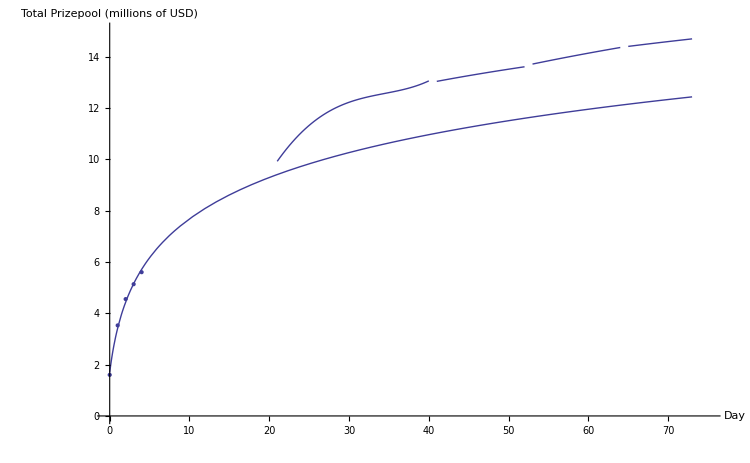

14.6875

```mathematica
proportional=1.34267
TI5extrapolate2=proportional*Log2P
TI5extrapolate3=proportional*Log3P
TI5extrapolate4=proportional*Log4P
TI5extrapolate5=proportional*Log5P
TI52P=Plot[TI5extrapolate2,{x,21,40},PlotRange->{{0,75},{0,15}}];
TI53P=Plot[TI5extrapolate3,{x,41,52},PlotRange->{{0,75},{0,15}}];
TI54P=Plot[TI5extrapolate4,{x,53,64},PlotRange->{{0,75},{0,15}}];
TI55P=Plot[TI5extrapolate5,{x,65,73},PlotRange->{{0,75},{0,15}}];
Show[{TI52P,TI5Plot,TI5Logplot,TI53P,TI54P,TI55P},ImageSize->150*{5,3},LabelStyle->Directive[Black,Medium],AxesLabel->{"Day","Total Prizepool (millions of USD)"}]
TI5extrapolate5/.x->73
```